```mathematica
If[!NumberQ[makePallette],NotebookEvaluate[NotebookDirectory[]~~"visualVocabDefs.nb"],NotebookEvaluate[NotebookDirectory[]~~"vvClear.nb"]];
```

## Wavelet Transforms

```mathematica
credits
```

This notebook is part of A Visual Vocabulary for Image Processing. All rights are reserved by the authors, W. A. Sethares and C. R. Johnson, Jr. Last revised Jan 2017. All x-ray images are used with permission of the Van Gogh Museum and the Rijksmuseum, Amsterdam, The Netherlands. Please do not violate the trust of the museums that have provided access to their x-ray images by distributing this data in any form.

Wavelet transforms can be used as a kind of scale-aware filtering operation, decomposing an image into a succession of images which approximate and refine the image at a collection of different scales. Higher settings for the refinement level allow larger-scale features to be resolved.

```mathematica
TableForm[{{Hyperlink["ApproxAndRefine",{"visualVocabWavelets.nb","labelApproxAndRefine"}],labelApproxAndRefine},{Hyperlink["WaveletView",{"visualVocabWavelets.nb","labelWaveletView"}],labelWaveletView},{Hyperlink["WaveletThreshold",{"visualVocabWavelets.nb","labelWaveletThreshold"}],labelWaveletThreshold},{Hyperlink["WaveletEnhance",{"visualVocabWavelets.nb","labelWaveletEnhance"}],labelWaveletEnhance}}]
```

| The wavelet transform decomposes an image, approximating and refining it at different scales
 | All the levels of the wavelet decomposition are shown on the left, the right picks out a single image to enlarge
 | A common technique with wavelet data is to threshold, to set all the values that lie below some value to zero
 | Multiply the wavelet coefficients at the specifed level by the given factor, then invert

There are a variety of wavelet related functions for calculating (DiscreteWaveletTransform[ ], StationaryWaveletTransform[ ], InverseWaveletTransform[ ]) and manipulating (WaveletThreshold[ ], WaveletImagePlot[ ], WaveletMapIndexed[ ]) wavelet data.

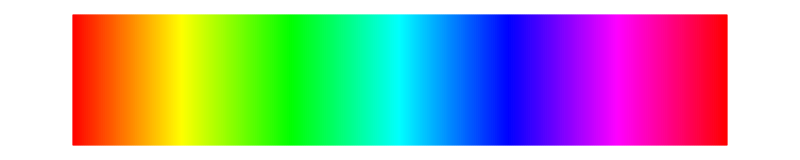

```mathematica
specLine
```

A common way to picture the action of a wavelet transform is as a single image that is divided into four pieces. The upper-right refinement corresponds to vertical components at the smallest scale (the highest frequency). The lower-left refinement corresponds to horizontal components at the smallest scale, the bottom-right corresponds to 45° components at the smallest scale. The upper left image would correspond to the approximation at this level -- but -- instead of picturing the approximation, the upper left is itself divided into four pieces. Again the upper-right is the vertical, the lower-left is the horizontal, and the lower-right is the diagonal, but now at the next smallest level. Again the upper-left of this block would contain the approximation, but instead contains another divided-into-four block. And so on, until the largest level (the smallest pictures) finally contains the approximation in the upper left.

```mathematica
labelApproxAndRefine="The wavelet transform decomposes an image,\napproximating and refining it at different scales";infoApproxAndRefine="Wavelet transforms decompose an image into a succession of images which approximate and refine the image at a collection of different scales. Higher settings for the refinement level allow larger-scale features to be resolved.\n\n For example, set the 'refinement level' slider to 1. This divides shows the wavelet transform as a single image divided into four pieces. The upper-right refinement corresponds to vertical components at the smallest scale (the highest frequency). The lower-left refinement corresponds to horizontal components at the smallest scale, the bottom-right corresponds to 45° components at the smallest scale. The upper left image corresponds to the approximation at this level.\n\nChange the refinement level to 2. Now all is the same as before -- but -- instead of picturing the approximation, the upper left is itself divided into four pieces. Again the upper-right is the vertical, the lower-left is the horizontal, and the lower-right is the diagonal, but now at the next smaller level.\n\nNow change the refinement level to 3. Again the upper-left of this block would contain the approximation, but instead contains another divided-into-four block.\n\nAnd so on, until the largest level (the smallest pictures) finally contains the approximation in the upper left.";Manipulate[WaveletImagePlot[DiscreteWaveletTransform[ImageResize[allImagesColor[[i]],{400}],HaarWavelet[]],n],
Row[{Control[{{i,vermeerStreet,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],info[infoApproxAndRefine]}],
Control[{{n,3,"refinement level"},1,7,1,Appearance->"Labeled"}],
FrameLabel->Style[labelApproxAndRefine,Medium],TrackedSymbols->{i,n},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

Another way to display the information is to show all the levels, all the refinements, and all the approximations. Here we can see all the images resized to the same smallness. One is picked out (by the slider called “Component to Enlarge”) for closer viewing.

```mathematica
labelWaveletView="All the levels of the wavelet decomposition are shown on the left, the right picks out a single image to enlarge";infoWaveletView="This interactive example contains exactly the same information as the previous example, though the data is displayed differently. Instead of making the pictures smaller and smaller at higher refinement levels, all are displayed at the same physical size on the left.\n\nFor a refinement level of 1 there are four images, a refinement level of 2 gives 8 images, a refinement level of 3 gives 12, etc.\n\nThe innovation here is to pick one of these (chosen by the 'component to enlarge' slider) and display this image on the right hand side where it can be clearly seen.\n\nAlso, instead of always using the default Haar wavelet, the popup menu allows selection from a variety of wavelet basis functions.";Manipulate[If[j>4 n,j=4 n];Row[{WaveletImagePlot[dw=DiscreteWaveletTransform[ImageResize[allImagesColor[[i]],{400}],waveletType, n],ImageSize->80,PlotLayout->"Grid"],Spacer[20],Labeled[Image[dw[All,"Image"][[j,2]],ImageSize->350],"Component "~~ToString[dw[All,"Image"][[j,1]]]]}],
Row[{Control[{{i,vermeerStreet,"image"},Thread[Range[numFilesC]->imageNamesC],ControlType->PopupMenu}],Spacer[20],
Control[{{waveletType,HaarWavelet[],"wavelet"},{HaarWavelet[],DaubechiesWavelet[2],DaubechiesWavelet[4],SymletWavelet[2],BattleLemarieWavelet[3],BiorthogonalSplineWavelet[4,2],CoifletWavelet[3],CDFWavelet[],MeyerWavelet[4],ShannonWavelet[],ReverseBiorthogonalSplineWavelet[2,4]}}]}],
Row[{Control[{{n,3,"refinement level"},1,7,1,Appearance->"Labeled"}],Spacer[20],
Control[{{j,1,"component to enlarge"},1,4 n,1,Appearance->"Labeled"}],Spacer[20],info[infoWaveletView]}],
FrameLabel->Style[labelWaveletView,Medium],
TrackedSymbols->{i,j,n,waveletType},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

```mathematica
labelWaveletThreshold="A common technique with wavelet data is to threshold, to set all the values that lie below some value to zero";
infoWaveletThreshold="As seen above, there are many images produced in a wavelet transform. One technique to use these images is to threshold one of the images. This will take features at that scale and remove all small values completely.\n\nIn this example, ";
Manipulate[img=allImagesXray[[i]];
dwd=DiscreteWaveletTransform[img,waveletType];
If[method=="Threshold",opt={"Firm",n},opt=method];
thr=WaveletThreshold[dwd,opt];
Row[{Labeled[Image[img,ImageSize->{250}],Text@"original"],Spacer[20],Labeled[Image[inv=InverseWaveletTransform[thr,waveletType],ImageSize->{250}],Text@"smoothed"],Spacer[20],Labeled[ImageAdjust[Image[ImageSubtract[img,inv],ImageSize->{250}]],Text@"difference"]}],
Row[{Control[{{i,cracks,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[20],Control[{{waveletType,CDFWavelet[],"wavelet"},{HaarWavelet[],DaubechiesWavelet[2],DaubechiesWavelet[4],SymletWavelet[2],BattleLemarieWavelet[3],BiorthogonalSplineWavelet[4,2],CoifletWavelet[3],CDFWavelet[],MeyerWavelet[4],ShannonWavelet[],ReverseBiorthogonalSplineWavelet[2,4]}}]}],Row[{Control[{{method,"Threshold","method"},{"Threshold","FDR","GCV","GCVLevel","SURE","SURELevel","SUREShrink","Universal","UniversalLevel","VisuShrink","VisuShrinkLevel"}}],Spacer[20],Control[{{n,0.5,"threshold value"},0,1}],Spacer[20],info[infoWaveletThreshold]}],
FrameLabel->Style[labelWaveletThreshold,Medium],TrackedSymbols->{i,waveletType,method,n},SaveDefinitions->saveDef]
```

```mathematica
specLine
```

-Graphics-

In the same way that ImageApply[ ] applies any specified function to the pixel values of an image, WaveletMapIndexed[ ] applies any specified function to the values of the DWT data. This demonstration multiplies all the coefficients at the specified level by a specified factor. Several aspects become clearer by playing around with these values. First, the levels that contain all zeros have no effect on the reconstruction (these are the approximation levels). The levels that end in 1 represent vertical filterings, the levels that end in 2 represent horizontal filterings, and the levels that end in 3 represent filterings at 45° angles. The more zeros in front, the larger the resulting features (the larger the scale, the lower the frequency).

```mathematica
labelWaveletEnhance="Multiply the wavelet coefficients at the specifed level by the given factor, then invert";
infoWaveletEnhance="In linear filtering, it is common to boost/multiply/amplify the information in a specified frequency range. This interactive example boosts the information in a specified scale range.\n\nThe technique is to pick a given level, multiply the wavelet coefficients at that level by a constant, and then take the inverse wavelet transform.\n\nApplying this to a number of different images leads to a variety of effects.\n\nWith the default settings, the level {0,0,2} of tile F634Tile is multiplied by a large number (20). This emphasizes horizontal features.\n\nWhich level should show similar vertical features? (try {0,0,1}).";
Manipulate[swt=StationaryWaveletTransform[imgX=allImagesXray[[i]],ShannonWavelet[]];
mapWave=WaveletMapIndexed[ImageMultiply[#,m]&,swt,level];
GraphicsRow[{imgX,InverseWaveletTransform[mapWave,ShannonWavelet[]]},ImageSize->700],
Row[{Control[{{i,f634Tile,"image"},Thread[Range[numFilesX]->imageNamesX],ControlType->PopupMenu}],Spacer[10],Control[{{level,{0,0,2},"multiply level"},Dynamic[swt[All][[All,1]]]}],Spacer[5],Control[{{m,20,"by"},0.1,40,Appearance->"Labeled"}],Spacer[20],info[infoWaveletEnhance]}],
FrameLabel->Style[labelWaveletEnhance,Medium],SynchronousUpdating->False,ContinuousAction->False,TrackedSymbols->{i,m,level},SaveDefinitions->saveDef]
```